# Part III Realizing image transfer process i) using speaker & microphone ii) connecting speaker output to microphone input externally

## This part is realizing transfer of the image where data carried by mechanical vibration (sound) and electrical signal. The below result obtained via letter way.

Here is to capture the data sent from the transmitter code in the other nb file. For instance, one can start recording sound from below code, and then play the prepared final audio from the other file.
The remaining part is the same with the Part II but the recorded raw sound contains noise due to the real data transport.
The code can be utilized  to realize analog image transfer with different ways including EM radiation, laser, near field E- and B- field. External transmitter and receiver parts can be modified by considering headset output of PC as a signal voltage source, and microphone input as probe measuring the signal.

```mathematica
a=AudioCapture[SampleRate->192000]
```

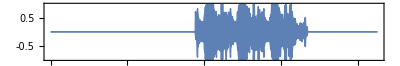

```mathematica
AudioPlot[a]
```

```mathematica
loudIntervals=AudioIntervals[AudioAmplify[a,5],#RMSAmplitude>.4&,.4]
```

{{3.79712,4.60996},{4.6564,5.46924},{5.49247,6.32853}}

```mathematica
rr=AudioTrim[a,loudIntervals][[1]];
gg=AudioTrim[a,loudIntervals][[2]];
bb=AudioTrim[a,loudIntervals][[3]];

arr=Spectrogram[AudioAmplify[rr,0.7],PlotRange->{All,{1000,21000}}, AspectRatio->1,Frame->None];
agg=Spectrogram[AudioAmplify[gg,0.7],PlotRange->{All,{1000,21000}}, AspectRatio->1,Frame->None];
abb=Spectrogram[AudioAmplify[bb,0.7],PlotRange->{All,{1000,21000}}, AspectRatio->1,Frame->None];
g={arr,agg,abb}

imgr=Binarize[arr,.6];
imgg=Binarize[agg,.6];
imgb=Binarize[abb,.6];

res=ImageAdjust[ColorNegate[ColorCombine[{imgr,imgg,imgb},"RGB"]]];
ImageResize[res,ImageDimensions[img]]
```

{-Graphics-,-Graphics-,-Graphics-}

-Graphics-